Extracting fluorescence lifetime information from photon bursts

Theorypaclet:Fretica/tutorial/ExtractingFluorescenceLiftimeInformationFromPhotonBursts#29460952 | Application to the TTTR-simulation of the IDPspaclet:Fretica/tutorial/ExtractingFluorescenceLiftimeInformationFromPhotonBursts#45074055

```mathematica
Needs["Fretica`"]
```

Theory

### Motivation: What do we learn from fluorescence lifetimes in FRET?

-Graphics-ϵ=k_ET/(k_D+k_ET)=k_ET/k_DA

Let us assume that we have a burst of duration T with N_A, N_D  acceptor and donor fluorescence photons.
From the photons we  can calculate:
	E=N_A/(N_A+N_D)
and
	τ = ∑_(i=1)^N_D δt_i/N_D ,
where  δt_i are the donor delay times after pulsed excitation (micro times).

Let us assume an ideal experiment (without background, γ=1, no crosstalk, IRF=delta function δ(t))

#### Static inter-dye distance (on timescale of a burst) with transfer efficiency ϵ

⟨E⟩=⟨N_A/(N_A+N_D)⟩=ϵ
⟨τ⟩/τ_D^0=τ_D/τ_D^0=1-ϵ

The fluorescence lifetime decay (i.e. the distribution of photon delay times)  is given by
P(δt)=k_DA exp (-k_DAδt )

⟨τ⟩=∫_0^∞ δt P(δt)ⅆδt =τ_D=1/k_DA

#### Dynamic inter-dye distance: 2-state system

Let’s now assume fast dynamics: 
faster than the interphoton times ( >μs ) , but slower than the fluorescence lifetime (ns).

Further we assume that the systems interconverts between two states with inter-dye distances r1 and r2:
ϵ_1⇄ ϵ_2
with equilibrium concentrations c_1 and c_2

⟨E⟩=c_1 ϵ_1+c_2 ϵ_2

P(δt)=(Q_1 c_1  k_DA_1 exp (-k_DA_1δt ) + Q_2 c_2  k_DA_2 exp (-k_DA_2δt ))/(Q_1 c_1+Q_2 c_2)

With the quantum yields
Q_i=(Q_D k_D)/k_DA_i=Q_D k_D τ_DA  ( Q_D : quantum yield of the donor)
we get
P(δt)=(c_1  exp (-k_DA_1δt ) + c_2  exp (-k_DA_2δt ))/(c_1 τ_D1 + c_2 τ_D2)

The mean fluorescence lifetime is then:

⟨τ⟩=∫_0^∞ δt P(δt)ⅆδt=(c_1 τ_D1^2 + c_2 τ_D2^2)/(c_1 τ_D1 + c_2 τ_D2)
or using τ_D_i=τ_D^0(1-ϵ_i)

⟨τ⟩=τ_D^0(c_1 (1-ϵ1)^2 + (c_2(1-ϵ2))^2)/(c_1 (1-ϵ1 )+ c_2 (1-ϵ2 ))

#### Dynamic inter-dye distance with continuous distribution p(r)

⟨ϵ⟩=∫_0^∞ ϵ(r)p(r)ⅆr

P(δt)=(∫_0^∞ p(r)exp (-k_DA(r)δt )ⅆr)/(∫_0^∞ p(r)/k_DA(r)ⅆr)

⟨τ⟩/τ_D^0=(∫_0^∞ p(r)( 1-ϵ(r) )^2 ⅆr)/(∫_0^∞ p(r)( 1-ϵ(r) ) ⅆr)=(⟨( 1-ϵ )^2⟩_r)/(⟨( 1-ϵ )⟩_r)= ... =1-⟨ϵ ⟩+(⟨ϵ^2 ⟩-⟨ϵ ⟩^2)/(1-⟨ϵ ⟩)  
	
This leads to
τ_D/τ_D^0=1-⟨ϵ⟩+σ_c^2/(1-⟨ϵ⟩)
	
with	σ_c^2=⟨ϵ^2⟩-⟨ϵ⟩^2 

Conclusion: ⟨τ⟩/τ_D^0 is for a dynamic system by σ_c^2/(1-⟨ϵ⟩)larger than for a static system.

A similar equation holds for the acceptor lifetime.
Here we have:
	 P_A(δt)∝(1- exp (-k_DA(r)δt ) )exp (-k_Aδt )
And we get:

(τ_A-τ_A^0)/τ_D^0=1-⟨ϵ⟩-σ_c^2/⟨ϵ⟩

#### Example: IDP with p(r)=Gaussian chain and dynamics on 10-100 ns scale

```mathematica
Pgc[rrms_][r_]:=(3/(2π))^(3/2)(4π)/rrms(r/rrms)^2 Exp[-3/2 (r/rrms)^2]
```

```mathematica
(*Normalization*)
Integrate[Pgc[rrms][r],{r,0,∞},Assumptions->{rrms>0}]
```

1

```mathematica
(* ⟨r^2⟩= *)
Integrate[r^2 Pgc[rrms][r],{r,0,∞},Assumptions->{rrms>0}]
```

rrms^2

```mathematica
Manipulate[Plot[Pgc[rrms][r],{r,0,10},GridLines->{{{rrms,Red}}, None},PlotRange->All,PlotLabel->"Gaussian chain distribution, ⟨r^2⟩^(1/2) = "<> ToString[rrms]],{{rrms,1},0.001,10}]
```

```mathematica
ϵ[r_]:=(1/(1+(1/r)^-6))
```

```mathematica
rfromE[e_]:=(1-e)^(1/6)/e^(1/6)
```

```mathematica
Emean[p_]:=NIntegrate[ϵ[r]p[r],{r,0,∞}]
```

```mathematica
Esqrmean[p_]:=NIntegrate[ϵ[r]^2 p[r],{r,0,∞}]
```

Variable transformation: P(r)→P(ϵ)

```mathematica
Pgc2[rrms_][e_]=Pgc[rrms][rfromE[e]]D[rfromE[e]]
```

(3 √(1-e) ⅇ^(-(3 (1-e)^(1/3))/(2 e^(1/3) rrms^2)) √(6/π))/(√e rrms^3)

```mathematica
Manipulate[GraphicsColumn[{Plot[Pgc[rrms][r],{r,0,4},GridLines->{{{rrms,Red}}, None},PlotRange->All,PlotLabel->"Gaussian chain distribution, ⟨r^2⟩^(1/2) = "<> ToString[rrms],AxesLabel->{"r/R_0","P(r/R_0)"}],Plot[Pgc2[rrms][e],{e,0.001,0.999},GridLines->{{{Emean[Pgc[rrms]],Red}}, None},PlotRange->All,PlotLabel->"P(ϵ) for GC, ⟨ϵ⟩ = "<> ToString[Emean[Pgc[rrms]]],AxesLabel->{"ϵ","P(ϵ)"}]}],{{rrms,1},0.001,10}]
```

```mathematica
τDvsE[p_]:=Module[{emean=Emean[p],esqmean=Esqrmean[p]},{emean,1-emean+(esqmean-emean^2)/(1-emean)}]
```

```mathematica
τAvsE[p_]:=Module[{emean=Emean[p],esqmean=Esqrmean[p]},{emean,1-emean-(esqmean-emean^2)/emean}]
```

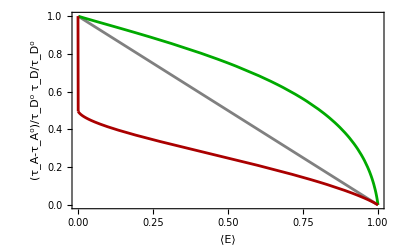

```mathematica
rrmsdye=1/5.4;(*in untis of R0*)
pltE=Show[
Plot[1-e,{e,0,1},PlotStyle->Directive[Gray,AbsoluteThickness[2]]],
ParametricPlot[τDvsE[Pgc[rrms]],{rrms,0.1,10},PlotRange->All,AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Green,AbsoluteThickness[2]]],
ParametricPlot[τAvsE[Pgc[rrms]],{rrms,0.1,15},PlotRange->{0,1},AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Red,AbsoluteThickness[2]]],ListLinePlot[{{0,1},τAvsE[Pgc[15]]},PlotStyle->Directive[Darker@Red,AbsoluteThickness[2]]],

Frame->True,FrameLabel->{"⟨E⟩","(τ_A-τ_A^0)/τ_D^0       τ_D/τ_D^0"},FrameStyle->Directive[Thick,FontSize[18]],LabelStyle->{FontFamily->"Helvetica",FontSize->18,FontWeight->Bold}
]
```

#### Influence of dye linker dynamics for “static case” ?

```mathematica
pdyeonstick[L_,rrms_][r_]:=(√(6/π) r/2 (Exp[-1/2 3/rrms^2(L-r)^2]-Exp[-1/2 3/rrms^2(L+r)^2]))/(L rrms)
```

```mathematica
Manipulate[Plot[{pdyeonstick[L,rrms][r],Pgc[rrms][r]},{r,0,15},PlotRange->All,PlotPoints->200],{L,0.1,10},{rrms,0.1,5}]
```

Dye linker r_rms=0.2 R_0

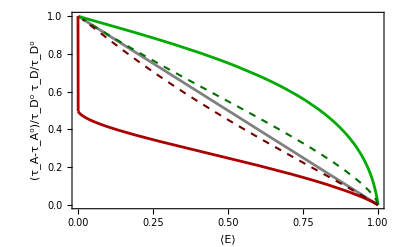

```mathematica
rrmsdye=0.2;(*in untis of R0*)
absthickness=1.5;
pltEstick[rrmsdye_]:=Show[pltE,
ParametricPlot[τDvsE[pdyeonstick[L,rrmsdye]],{L,0.01,2},PlotRange->All,AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Darker@Green,AbsoluteThickness[absthickness],Dashed]],
ParametricPlot[τAvsE[pdyeonstick[L,rrmsdye]],{L,0.01,2},PlotRange->{0,1},AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Darker@Red,AbsoluteThickness[absthickness],Dashed]]
]
pltEstick[rrmsdye]
```

Dye linker r_rms=0.5 R_0

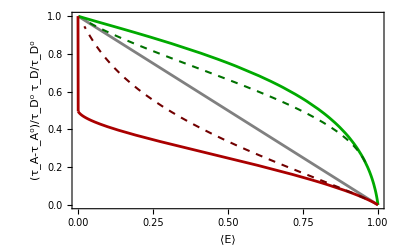

```mathematica
rrmsdye=0.5;(*in untis of R0*)
pltEstick[rrmsdye]
```

### Problem: τ needs to be corrected for background and for the IRF

#### Equations

The measured photon-delay distribution can be written (with δt=t)  like

h(t) =(n_f(f⊗g)(t)+ n_b bg(t))/(n_f+ n_b)

where:
f(t) :  fluorescence decay
g(t):=IRF with g(t+T)=g(t) (periodic)

bg(t):= distribution of background photons
n_f: fluorescence rate
n_b: background rate

(f⊗g)(t) is a circular convolution defined by:
(f⊗g)(t)=∫_0^T f(t_1)g(t-t_1)ⅆ t_1

#### circular convolution

```mathematica
g[t0_,σ_,T_][t_]=Sum[PDF[NormalDistribution[t0,σ],t-i T],{i,-5,5}];
```

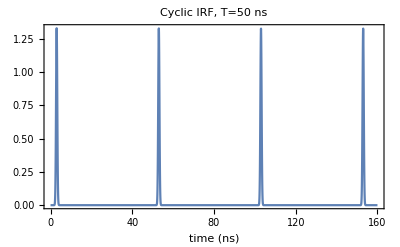

```mathematica
Plot[g[3,0.3,50][t],{t,0,160},PlotRange->All,Frame->True, PlotLabel->"Cyclic IRF, T=50 ns",FrameLabel->{"time (ns)",""}]//Quiet
```

```mathematica
f[kD_][t_]=kD Exp[-kD t];
f[T_,kD_][t_]=kD Exp[-kD t]+kD Exp[-kD (t+T)];
```

```mathematica
demo1[kD_,t0_,σ_]:=Module[{T=25,dt=0.05,times,irf,F,c,Addt},
times=Table[t,{t,0,T,dt}];
Addt[ydat_]:={times,ydat}ᵀ;
irf=Table[g[t0,σ,T][t],{t,0,T,dt}];irf/=Total[irf];
F=Table[f[T,kD][t],{t,0,T,dt}];F/=Total[F];
c=ListConvolve[irf,F,1];
Addt/@{F/Max[F],irf/Max[irf],c/Max[c]}
]
Manipulate[
ListLinePlot[demo1[kD,t0,σ],PlotRange->All,PlotLabel->"Circular convolution",PlotLegends->Placed[{"f(t)","IRF(t)", "(f⊗IRF)(t)"},{Right,Center}]]//Quiet
,{{kD,0.25},0.02,1}
,{{t0,3},0,25}
,{{σ,0.2},0.02,10}
]
```

#### Method 1 : Needs ⟨t⟩_IRF and ⟨t⟩_bg

⟨t⟩_h =∫_0^T t h(t)ⅆt=(n_f ⟨t⟩_(f⊗g) + n_b ⟨t⟩_bg)/(n_f+ n_b)

One can show that:
⟨t⟩_(f⊗g)= ⟨t⟩_f+ ⟨t⟩_g-T∫_0^T f(t)  ∫_0^t g(T-t_1)ⅆ t_1ⅆt
	          ≃ ⟨t⟩_f+ ⟨t⟩_g , if the IRF is narrow, ⟨t⟩_g<<T

⟨t⟩_h =(n_f( ⟨t⟩_f+ ⟨t⟩_g ) + n_b ⟨t⟩_bg)/(n_f+ n_b)

Solving for ⟨t⟩_f leads to the important result:

⟨t⟩_f ≃(⟨t⟩_h  - α ⟨t⟩_bg)/(1-α)- ⟨t⟩_IRF with α=n_b/(n_f+ n_b)

If  f(t→T)≃0 then ⟨t⟩_f=⟨τ⟩, otherwise ⟨t⟩_f needs to be corrected for the fact that  T is not long enough to include the complete decay. 

For a burst of duration Δ with N'_D photon counted in the donor channel (not corrected for background)
 one can estimate:

τ=(τ'  - α ⟨t⟩_bg)/(1-α)- ⟨t⟩_IRF with τ' = ∑_(i=1)^N'_D δt_i/N'_D and  α=(nb Δ)/N'_D 

Only ⟨t⟩_bg and ⟨t⟩_IRF needs to be known before.

#### Method 2 : (MLH) approach. Needs full IRF and background distributions.

In the experiment δt is discretized. Every photons falls into a microtime channel c such that 
c dt ≤δt<(c+1)dt , with c=0,... c_max
 where dt is the time resolution of the counting electronics (e.g. dt=16 ps).
 
The probability that a photon falls into channel c is given by
p(c) =h( c  dt)  dt.

In every burst we measure a distribution  of donor photons {N_0, N_1, ... ,N_cmax} with ∑_(c=0)^cmax N_c=N'_D , where N_c is the number of photons falling into channel c.

The probability of this distribution given N_D and the model, i.e. given  h(t), is then:

p( { N_0,...,N_cmax} | N'_D; h(t) )  =  ∏_(c=0)^c_max (p(c))^N_c  

We can define the logarithmic likelihood of the model by
l( h(t) )=ln[p( { N_0,...,N_cmax} | N_D; h(t) )]= ∑_(c=0)^cmax N_c ln(p(c)) 

We can maximize the likelihood with respect to the model parameters of  f(t) for obtaining the most likely parameter values.

However, here we are only interested in the mean fluorescence lifetime, in this case it is enough to maximize the likelihood with respect to τ for
f(t)=1/τ exp(-t/τ)
even if the true decay is not single exponential. 

The model for h is then:
h(t) =(1-α)(f⊗IRF)(t)+ α bg(t) with α=(nb Δ)/N'_D
The IRF and bg(t) need to be known.

Application to the TTTR-simulation of the IDPs

### Preliminaries

```mathematica
Needs["Fretica`"]
```

```mathematica
cfunc[color_]:=(If[#==0.,RGBColor[1, 0, 0,0],Lighter[color,1-#]]&)
```

```mathematica
rrmsdye=1/5.4;(*in untis of R0*)
pltSvsE=pltEstick[rrmsdye];
```

### Settings and burst identification

```mathematica
FOpenTTTR[$FreticaExamples<>"\\SimIDPBinding2.ht3"]
```

1

```mathematica
γ=1.2; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
G=0.95;
rcm=({{1, -ct, 0, 0}, {0, γ, 0, 0}, {0, 0, G, -G ct}, {0, 0, 0, G γ}});
pieγ= 1.2;
```

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
FEnablePie[True];
FSetPIEGamma[pieγ];
FSetFRETRoutes[{"A","D","A","D"}];
FSetAnisotropyRoutes[{"P","P","S","S"},{"P","P","S","S"}]
FSetAnisotropyL1[0];
FSetAnisotropyL2[0];
FSetPIERoutes[FGetAcceptorRoutes[]];
FSetChannelConstraints[chmain={1,1500}];
FSetPIEChannelConstraints[chpie={1500,3000}];
```

```mathematica
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,20,10000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold];
FDetermineBackground[];
bgdecays=FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->FNonBursts  (*Default*),FOutput->FData];
bgrates=FDetermineBackground[]
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
FFindBurstsDeltaT[0.00015,80,10000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
```

{1083.69,948.398,1092.88,919.328,0.,0.}

{763.338,763.381,764.203,759.231,0.,0.}

{763.338,763.381,764.203,759.231,0.,0.}

8515

5782

```mathematica
FCalcBurstLifeTimes[1,0,0,25];
FCalcBurstLifeTimes[2,0,0,25];
FCalcBurstLifeTimes[3,0,0,25];
FCalcBurstLifeTimes[4,0,0,25];
kD=0.25;
kA=0.25;
```

### Lifetime histograms

#### Lifetime bound

```mathematica
FSelectBursts[{"Epie","Spie"},0.65<#[[1]]&& 0.3<#[[2]]&]
```

1

```mathematica
FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->FSelectedBursts]
```

-Graphics-

```mathematica
{iAp,iDp,iAs,iDs}=FLifeTimeHisto[FRoutes->{1,2,3,4},FOutput->FData,FPhotonData->FSelectedBursts][[All,1;;1500]]  ;
```

```mathematica
itotA=iAp+2 G  iAs;
itotA[[All,1]]=iAp[[All,1]];
itotD=iDp+2 G  iDs;
itotD[[All,1]]=iDp[[All,1]];
ItotABound=itotA;
ItotDBound=itotD;

ListLogPlot[{ItotABound,ItotDBound},PlotRange->All,Frame->True]
```

-Graphics-

#### Lifetime free

```mathematica
FSelectBursts[{"Epie","Spie"},0.3<#[[1]]<0.6&& 0.3<#[[2]]&]
```

1

```mathematica
FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->FSelectedBursts]
```

-Graphics-

```mathematica
{iAp,iDp,iAs,iDs}=FLifeTimeHisto[FRoutes->{1,2,3,4},FOutput->FData,FPhotonData->FSelectedBursts][[All,1;;1500]]  ;
```

```mathematica
itotA=iAp+2 G  iAs;
itotA[[All,1]]=iAp[[All,1]];
itotD=iDp+2 G  iDs;
itotD[[All,1]]=iDp[[All,1]];
ItotAFree=itotA;
ItotDFree=itotD;
```

```mathematica
plLiftime=ListLogPlot[{ItotDFree,ItotDBound},PlotRange->All,Frame->True,FrameLabel->{"delay time (ns)", "Donor photon counts"}]
```

-Graphics-

```mathematica
ListLogPlot[{ItotAFree,ItotABound},PlotRange->All]
```

-Graphics-

#### Background distribution and IRF from non-burst photons

```mathematica
bgDonorDecay=Mean[bgdecays[[FGetRoutes["D"],Span@@chmain]]];
bgAcceptorDecay=Mean[bgdecays[[FGetRoutes["A"],Span@@chmain]]];
```

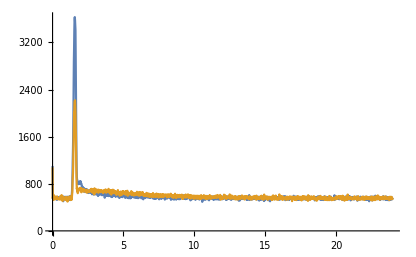

```mathematica
ListPlot[{bgDonorDecay,bgAcceptorDecay},Joined->True,PlotRange->All]
```

```mathematica
tmeanBgD=Total[bgDonorDecay[[All,2]](Range[Length[bgDonorDecay]])0.016]/Total[bgDonorDecay[[All,2]]]
tmeanBgA=Total[bgAcceptorDecay[[All,2]](Range[Length[bgAcceptorDecay]])0.016]/Total[bgAcceptorDecay[[All,2]]]
```

11.3219

11.4578

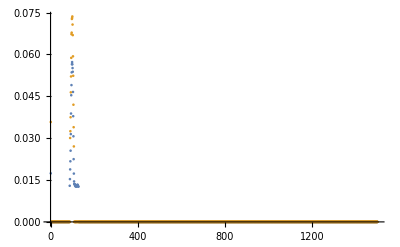

```mathematica
irfD=bgDonorDecay[[All,2]]/.y_/;y<800->0;
irfD[1]=0;
irfD/=Total[irfD];

irfA=bgAcceptorDecay[[All,2]]/.y_/;y<800->0;
irfA[1]=0;
irfA/=Total[irfA];
ListPlot[{irfD,irfA}]
```

```mathematica
tmeanIRFD=Total[irfD(Range[Length[irfD]])0.016]/Total[irfD]
tmeanIRFA=Total[irfA(Range[Length[irfA]])0.016]/Total[irfA]
```

1.62042

1.52218

```mathematica
bgD=bgrates[[2]]+bgrates[[4]]
bgA=bgrates[[1]]+bgrates[[3]]
```

1522.61

1527.54

### Method 1: τ_D vs E

#### Get anything needed from the bursts

τ=(τ'  - α ⟨t⟩_bg)/(1-α)- ⟨t⟩_IRF with τ' = ∑_(i=1)^N'_D δt_i/N'_D and  α=(nb Δ)/N'_D

```mathematica
FSelectBursts[{"Spie"},#[[1]]>0.3&];
{et,taumeanA,taumeanD,awA,awD}=FGetFromBurstList[Hold@{"Epie",("n1""tau1"+2G"n3""tau3")/("n1"+2G"n3"+0.001),("n2""tau2"+2G"n4""tau4")/("n2"+2G"n4"),"BurstDuration"bgA/("nA_raw"+0.1),"BurstDuration"bgD/("nD_raw")},FBurstData->FSelectedBursts];
```

#### Calculation with background correction :

```mathematica
tauD=(taumeanD-awD tmeanBgD)/(1-awD)-tmeanIRFD;
tauD*=kD;
```

```mathematica
ptdonly=Mean@Select[{et,tauD }ᵀ,#[[1]]<0.2&];
dptdonly=StandardDeviation@Select[{et,tauDA kD}ᵀ,#[[1]]<0.2&];
ptdonly=Around@@@Transpose[{ptdonly,dptdonly}]
ptfree=Mean@Select[{et,tauD }ᵀ,0.2<#[[1]]<0.65&];
ptbound=Mean@Select[{et,tauD }ᵀ,0.7<#[[1]]&];
dptfree=StandardDeviation@Select[{et,tauD}ᵀ,0.2<#[[1]]<0.65&];
dptbound=StandardDeviation@Select[{et,tauD}ᵀ,0.7<#[[1]]&];
ptfree=Around@@@Transpose[{ptfree,dptfree}]
ptbound=Around@@@Transpose[{ptbound,dptbound}]

pl1=Show[pltSvsE,
Histo2D[{et,tauD }ᵀ,{-0.2,1.0,.03},{-0.2,1.4,0.1},PlotRange->All,Contours->5,ColorFunction->cfunc[RGBColor[0, 1, 0,0.5]],ClippingStyle->{Pink,Black}]
,pltSvsE,ListPlot[{ptdonly,ptfree,ptbound},PlotStyle->Lighter@Blue],AspectRatio->1,PlotRange->{{-0.1,1.1},{-0.1,1.1}},Axes->False]
```

{0.00489991StandardDeviation[Transpose[]],0.984619StandardDeviation[Transpose[]]}

{0.500.05,0.760.15}

{0.800.04,0.320.27}

-Graphics-

```mathematica
tauA=(taumeanA-awA tmeanBgA)/(1-awA)-tmeanIRFA;
tauA=kD(tauA-1/kA);
```

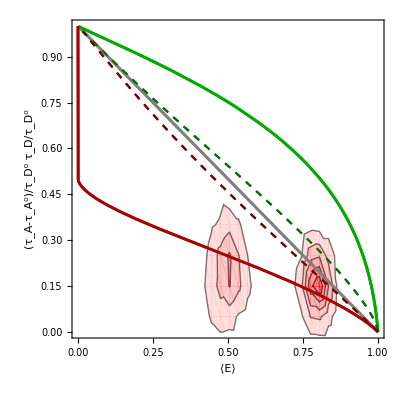

```mathematica
pl2=Show[pltSvsE,Histo2D[{et,tauA }ᵀ,{-0.2,1.0,.03},{-0.2,1.4,0.1},PlotRange->All,Contours->5,ColorFunction->cfunc[RGBColor[1, 0, 0,0.5]]],pltSvsE,AspectRatio->1]
```

```mathematica
Show[pl2,pl1,ListPlot[{ptdonly,ptfree,ptbound},PlotStyle->Lighter@Blue],PlotRange->{{-0.1,1.1},{-0.1,1.1}},Axes->False]
```

-Graphics-

### Method 2: τDA vs E calculation using maximum entropy estimator:

#### Definitions

```mathematica
Clear[Maxloglh]
Maxloglh[irf_, bgdis_,chmax_,dt_][{et_,bgfraction_,phlist_}]:=Module[{th,fit,loglh,k},
th=BinCounts[phlist,{0,chmax,1}];
loglh[k_?NumericQ]:=Module[{Fm,cm},
Fm=k Exp[-k dt (Range[chmax]-0.5)];
Fm=ListConvolve[N@irf,Fm,1]; Fm/=Total[Fm];
cm=(1-bgfraction)Fm+bgfraction bgdis;
th.Log[cm]
];
loglh[0.2];
fit=Quiet@FindMaximum[loglh[Abs@k],{{k,0.2}}];
{et,1/Abs[k]/.fit[[2]]}
]
```

```mathematica
dt=0.016;
chmax=chmain[[2]]
```

1500

```mathematica
bglD=bgDonorDecay[[All,2]]/Total[bgDonorDecay[[All,2]]];
bglA=bgAcceptorDecay[[All,2]]/Total[bgAcceptorDecay[[All,2]]];
```

#### Get for all bursts the lifetime channels of the donor photons

```mathematica
FSelectBursts[{"Spie"},#[[1]]>0.3&];
bl=Transpose@FGetFromBurstList[Hold@{"Epie","BurstDuration"*bgD,Map[Cases[Transpose[#],{2|4,x_}/;x<chmax:>x]&,Transpose[{"DetectionChannels","LifeTimeChannels"}]]},FBurstData->FSelectedBursts];
bl[[All,2]]/=(Length/@bl[[All,3]]);
```

```mathematica
bl[[1]]
```

{0.444725,0.0734927,{294,1287,142,156,172,142,334,156,189,1019,304,116,255,506,102,99,376,737,354,174,1094,134,230,156,274,144,264,367,186,328,100,558,488,124,496,405,175,102,109,768}}

#### Maximize the likelihood function

```mathematica
evstauD=ParallelMap[Maxloglh[irfD[[1;;100]], bglD,chmax,dt],bl[[1;;]]];//AbsoluteTiming
evstauD[[All,2]]+=dt;
evstauD[[All,2]]*=kD;
(*evstauD=Select[evstauD,(-0.5<#[[2]]<2)&];*)
```

{10.9494,Null}

#### Do the same for acceptor photons

```mathematica
FSelectBursts[{"Epie","Spie"},#[[1]]>0.3&&#[[2]]>0.3&]
bl=Transpose@FGetFromBurstList[Hold@{"Epie","BurstDuration"*bgA,Map[Cases[Transpose[#],{1|3,x_}/;x<chmax:>x]&,Transpose[{"DetectionChannels","LifeTimeChannels"}]]},FBurstData->FSelectedBursts];
bl[[All,2]]/=(Length/@bl[[All,3]]);
```

1

```mathematica
evstauA=ParallelMap[Maxloglh[irfA[[1;;100]], bglA,chmax,dt],bl[[1;;]]];//AbsoluteTiming
evstauA[[All,2]]+=dt;
evstauA[[All,2]]=kD(evstauA[[All,2]]-1/kA);
```

{4.64999,Null}

#### And here are the result:

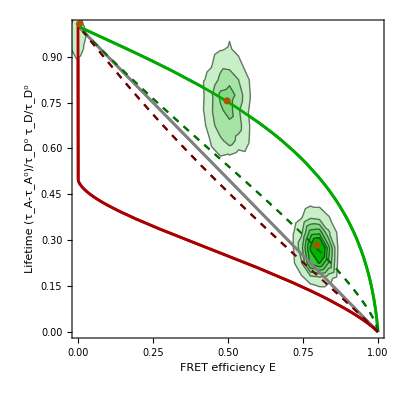

```mathematica
StandardError[data_]:=StandardDeviation[data]/√Length[data]
ptdonly=Mean@Select[evstauD,#[[1]]<0.2&];
dptdonly=StandardError@Select[evstauD,#[[1]]<0.2&];
ptdonly=Around@@@Transpose[{ptdonly,dptdonly}];
ptfree=Mean@Select[evstauD,0.2<#[[1]]<0.65&];
ptbound=Mean@Select[evstauD,0.7<#[[1]]&];
dptfree=StandardError@Select[evstauD,0.2<#[[1]]<0.65&];
dptbound=StandardError@Select[evstauD,0.7<#[[1]]&];
ptfree=Around@@@Transpose[{ptfree,dptfree}];
ptbound=Around@@@Transpose[{ptbound,dptbound}];

ptfreeA=Mean@Select[evstauA,0.2<#[[1]]<0.65&];
ptboundA=Mean@Select[evstauA,0.7<#[[1]]&];
dptfreeA=StandardError@Select[evstauA,0.2<#[[1]]<0.65&];
dptboundA=StandardError@Select[evstauA,0.7<#[[1]]&];
ptfreeA=Around@@@Transpose[{ptfreeA,dptfreeA}];
ptboundA=Around@@@Transpose[{ptboundA,dptboundA}];
plA=Histo2D[evstauA,{-0.05,1.05,.03},{-0.1,1.19,0.05},PlotRange->200,Contours->6,ColorFunction->(If[#==0.,RGBColor[1, 0, 0,0],Lighter[RGBColor[0.7, 0, 0,0.5],1-#]]&),ClippingStyle->Automatic];
plD=Histo2D[evstauD,{-0.05,1.05,.03},{-0.1,1.19,0.05},PlotRange->200,Contours->6,ColorFunction->(If[#==0.,RGBColor[0, 1, 0,0],Lighter[RGBColor[0, 0.7, 0,1],1-#]]&),ClippingStyle->Automatic];
plEvsTau=Show[pltSvsE,
plD,
pltSvsE,
ListPlot[{ptdonly,ptfree,ptbound},PlotStyle->Darker@Orange],

AspectRatio->1,FrameLabel->{"FRET efficiency E","Lifetime\n (τ_A-τ_A^0)/τ_D^0        τ_D/τ_D^0" }]
```

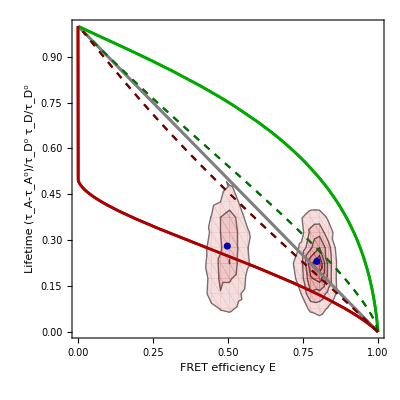

```mathematica
StandardError[data_]:=StandardDeviation[data]/√Length[data]
ptdonly=Mean@Select[evstauD,#[[1]]<0.2&];
dptdonly=StandardError@Select[evstauD,#[[1]]<0.2&];
ptdonly=Around@@@Transpose[{ptdonly,dptdonly}];
ptfree=Mean@Select[evstauD,0.2<#[[1]]<0.65&];
ptbound=Mean@Select[evstauD,0.7<#[[1]]&];
dptfree=StandardError@Select[evstauD,0.2<#[[1]]<0.65&];
dptbound=StandardError@Select[evstauD,0.7<#[[1]]&];
ptfree=Around@@@Transpose[{ptfree,dptfree}];
ptbound=Around@@@Transpose[{ptbound,dptbound}];

ptfreeA=Mean@Select[evstauA,0.2<#[[1]]<0.65&];
ptboundA=Mean@Select[evstauA,0.7<#[[1]]&];
dptfreeA=StandardError@Select[evstauA,0.2<#[[1]]<0.65&];
dptboundA=StandardError@Select[evstauA,0.7<#[[1]]&];
ptfreeA=Around@@@Transpose[{ptfreeA,dptfreeA}];
ptboundA=Around@@@Transpose[{ptboundA,dptboundA}];
plA=Histo2D[evstauA,{-0.05,1.05,.03},{-0.1,1.19,0.05},PlotRange->200,Contours->6,ColorFunction->(If[#==0.,RGBColor[1, 0, 0,0],Lighter[RGBColor[0.7, 0, 0,0.5],1-#]]&),ClippingStyle->Automatic];
plD=Histo2D[evstauD,{-0.05,1.05,.03},{-0.1,1.19,0.05},PlotRange->200,Contours->6,ColorFunction->(If[#==0.,RGBColor[0, 1, 0,0],Lighter[RGBColor[0, 0.7, 0,1],1-#]]&),ClippingStyle->Automatic];
plEvsTau=Show[pltSvsE,
plA,
pltSvsE,
ListPlot[{ptfreeA,ptboundA},PlotStyle->Darker@Blue],

AspectRatio->1,FrameLabel->{"FRET efficiency E","Lifetime\n (τ_A-τ_A^0)/τ_D^0        τ_D/τ_D^0" }]
```

| Related Guides
▪Fretica